# Guess Mystery Mass

## Last Updated: 2024/05/14

```mathematica
(*Quit[];*)
```

```mathematica
(*todo: allow multiple entry of freqs*)
(*todo: remove answers with negative frequencies*)
```

## User Input

```mathematica
(*bright ion mass*)
massDJ=40;
(*ion chain configuration*)
numBrightIons=1;
```

```mathematica
(*bright ion secular frequencies - axial, RF, EGGS*)
wsecList={710,1295.2,1580.8}*wkhz;
(*trap RF frequency*)
ωRF=19.0855*wmhz;
```

```mathematica
(*mystery mass search range*)
searchRange=Range[20,80,0.1];
```

```mathematica
(*known chain COM frequency*)
freqGuessMHz=1.4236;
```

## General

## Constants

```mathematica
(*fundamental*)
ℏ=1.0545718*^-34;
me=9.10938356*^-31;
qe=1.60217662*^-19;
c=2.99792458*^8;
kb=1.38064852*^-23;
```

```mathematica
(*derived*)
ke2=2.30707751*^-28;
a0=ℏ^2/me/ke2;
debye=1.*^-21/c;
amu=1.66053904*^-27;
```

## Units

```mathematica
{nm,μm,mm}={10.^-9,10.^-6,10.^-3};
```

```mathematica
{ns,us,ms}={10.^-9,10.^-6,10.^-3};
```

```mathematica
{khz,mhz,ghz}={10.^3,10.^6,10.^9};
{wkhz,wmhz,wghz}=2π*{10.^3,10.^6,10.^9};
```

```mathematica
{mv,uv}={10.^-3,10.^-6};
```

## Options

### Messages

```mathematica
(*turn off messages*)
Evaluate[
Off[General::munfl];
Off[LaunchKernels::nodef];
Off[InterpolatingFunction::dmval];
];
ParallelEvaluate[
Off[General::munfl];
Off[LaunchKernels::nodef];
Off[InterpolatingFunction::dmval];
];
```

### Plotting

```mathematica
(*set plot options*)
SetOptions[Plot,PlotRange->Automatic,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic(*,AspectRatio->Full*)];
SetOptions[ListPlot,PlotRange->Automatic,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large,GridLines->Automatic(*,AspectRatio->Full*)];
SetOptions[ListLinePlot,PlotRange->Automatic,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic(*,AspectRatio->Full*)];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

## Functions

### Helper Functions

```mathematica
(*get dimension (i.e. x, y, or z) of eigenvector for MotionalModes2 function*)
GetDimension[vec_]:=First@Ordering[
Norm/@ArrayReshape[vec,{3,Length[vec]/3}],
-1];
```

### Secular Frequency Calculation

```mathematica
(*secular frequency calculations*)
ωSecRadial[q_,a_,β_]:=β/2 Sqrt[q^2/2-a];
ωSecAxial[a_,β_]:=β/2 Sqrt[2*a];
ωSecXYZ[q_,ar_,az_,β_]:=β/2 Sqrt[{q^2/2-(az-ar),q^2/2-(az+ar),2*az}];
```

### Motional Mode Calculation

```mathematica
MotionalModes[mArr_List,xyzFreq_List,λ3_:0.0,λ4_:0.0]:=Module[
{
chainFreq=Transpose[xyzFreq],
numIons=Length[mArr],
scaleArr=Sqrt[KroneckerProduct[mArr,1/mArr]]*(xyzFreq[[;;,3]]^2),
z0eq,z0eqArr,
L0EQlist,guessz0eq,L0Mn,L0MnMat,
VMatX,VMatY,VMatZ
},

(*set up objects for equilibrium positions*)
z0eqArr = Array[z0eq,numIons];
L0EQlist=(z0eqArr[[#]]+(1.5*λ3)*z0eqArr[[#]]^2+(2.*λ4)*z0eqArr[[#]]^3)==(
Sum[(z0eqArr[[#]] - z0eqArr[[k]])^-2,{k,1,#-1}] 
- Sum[(z0eqArr[[#]] - z0eqArr[[k]])^-2,{k, #+1,numIons}]
)&/@Range[numIons];
(*guess axial equilibrium positions*)
guessz0eq=Range[-#,#,(2*#)/(numIons-1)]&[numIons^(1/3)]//N;
guessz0eq=Transpose[Join[{z0eqArr},{guessz0eq}]];
z0eqArr=z0eqArr/.Chop[FindRoot[L0EQlist,guessz0eq]];

(*format axial equilibrium positions into usable format*)
L0Mn=Abs[Table[If[i==j,0,(z0eqArr[[i]]-z0eqArr[[j]])^-3],{i,numIons},{j,numIons}]];
L0MnMat=DiagonalMatrix[Total[L0Mn,{2}]]-L0Mn;

(*extract secular frequencies*)
VMatZ=scaleArr*(DiagonalMatrix[(1+(3.*λ3)*#+(6.*λ4)*#^2)&/@z0eqArr]+2*L0MnMat);
VMatY=scaleArr*(DiagonalMatrix[(chainFreq[[2,;;]]/chainFreq[[3,;;]])^2]-L0MnMat);
VMatX=scaleArr*(DiagonalMatrix[(chainFreq[[1,;;]]/chainFreq[[3,;;]])^2]-L0MnMat);

(*return secular frequencies in usable form*)
{Sqrt[#[[;;,1]]],#[[;;,2]]}&[{Eigensystem[VMatX],Eigensystem[VMatY],Eigensystem[VMatZ]}]
];
```

```mathematica
(*this one accounts for stray fields but not anharmonicity*)
MotionalModes2[mArr_List,xyzFreq_List,(*λ3_:0.0,λ4_:0.0,*)offsetArr_List:{0.,0.,0.}]:=Module[
{
numIons=Length[mArr],
chainFreq=Transpose[xyzFreq],
scaleArr=Sqrt[KroneckerProduct[mArr,1/mArr]]*(xyzFreq[[;;,3]]^2),
l0=(ke2/(mArr[[-1]]*amu*xyzFreq[[-1,-1]]^2))^(1/3),
guessr0eq,r0eq,r0eqArr,r0eqArrFinal,L0EQlist,
L0Mn,R0Mn,trapFreqMat,
idMat,L0Mn2,L0MnMix,L0MnSelf,L0MnFinal,
res
},

(*set up infra to guess equilibrium positions*)
r0eqArr = Array[r0eq,{3,numIons}];
guessr0eq=Join[ConstantArray[0.,{2,numIons}],{Range[-1.,1.,2./(numIons-1.)]*numIons^(1./3.)}];
guessr0eq=Flatten[{r0eqArr,guessr0eq},{{2,3},{1}}];
(*set up force balancing equations for equilibrium positions*)
L0EQlist=Table[
(r0eqArr[[dim,ion]])==(chainFreq[[3,ion]]/chainFreq[[dim,ion]])^2*(Sum[(r0eqArr[[dim,ion]] - r0eqArr[[dim,k]])/(Norm[r0eqArr[[;;,ion]] - r0eqArr[[;;,k]]])^3,{k,Delete[Range[numIons],ion]}] )
+qe/(l0*amu)*offsetArr[[dim]]/(mArr[[ion]]*chainFreq[[dim,ion]]^2),
{dim,3},
{ion,numIons}
];

(*guess equilibrium positions*)
r0eqArrFinal=r0eqArr/.Chop[FindRoot[Flatten[L0EQlist],guessr0eq]];
(*r0eqArrFinal=Transpose[(#-offsetArr)&/@Transpose[r0eqArrFinal]];*)
(*Print[r0eqArrFinal];*)

(*format equilibrium positions into usable format*)
(*get R0Mn = (R^ij)^-1*)
R0Mn=Table[If[i==j,0,
(Norm[r0eqArrFinal[[;;,i]] - r0eqArrFinal[[;;,j]]])^-1
],{i,numIons},{j,numIons}];
(*get L0Mn = Subscript[R, α]^ij*)
L0Mn=Table[If[i==j,0,
r0eqArrFinal[[dim,i]] - r0eqArrFinal[[dim,j]]],
{dim,3},{i,numIons},{j,numIons}];

(*calculate trap frequency matrix*)
trapFreqMat=Table[If[iDim==jDim,
DiagonalMatrix[(chainFreq[[iDim]]/chainFreq[[3]])^2],
ConstantArray[0.,{numIons,numIons}]
],{iDim,3},{jDim,3}];

(*calculate Subscript[B, ij]*)
idMat=Outer[Times,IdentityMatrix[3],ConstantArray[1.,{numIons,numIons}]-IdentityMatrix[numIons],2,1];
L0Mn2=Outer[R0Mn^2*#1*#2&,L0Mn,L0Mn,1];
L0MnMix=Map[R0Mn^3*#&,idMat-3.*L0Mn2,{2}];
L0MnSelf=Map[DiagonalMatrix,Total[-L0MnMix,{4}],{2}];
L0MnFinal=Map[#*scaleArr&,L0MnSelf+L0MnMix+trapFreqMat,{2}];
(*Print[Flatten[L0MnFinal/wmhz^2,{1}]//MatrixForm];*)

(*get eigenvalues and eigenvectors*)
res=Transpose[{Sqrt[#[[1]]],#[[2]]}]&[Eigensystem[Flatten[L0MnFinal,{{1,3},{2,4}}]]];
(*sort eigenvalues by dimension*)
Return[Flatten[
Values[GroupBy[res,GetDimension[#[[2]]]&]],
{{3},{1},{2}}
]];
];
```

## Calculate

## Generate Potential Parameters

### Extract Mass-Independent Mathieu Parameters

```mathematica
(*get mathieu parameters from known secular frequencies*)
ar=(wsecList[[3]]^2-wsecList[[2]]^2)/(2*(ωRF/2)^2);(*Subscript[a, x,y] =±(4*e*Subscript[V, 0])/(m*Subscript[r, 0]^2*Ω^2)-(8*e*Subscript[U, DC])/(m*Subscript[z, 0]^2*Ω^2)*)
az=(2*wsecList[[1]]^2)/ωRF^2;(*Subscript[a, z] =(4*e*Subscript[U, DC])/(m*Subscript[z, 0]^2*Ω^2)*)
qx=Sqrt[2(wsecList[[3]]^2/(ωRF/2)^2+(az-ar))];(*Subscript[q, r] = (2*e*Subscript[V, RF])/(m*Subscript[r, 0]^2*Ω^2)*)
```

```mathematica
(*make parameters mass-independent*)
{qx0,ar0,az0}=(massDJ)*{qx,ar,az};
```

```mathematica
(*az0=0.1;
ar0=0.26;
qx0=9.32796;
*)
```

### Prepare Mode Parameters

```mathematica
(*convenience function to generate MotionalModes function input*)
mystParamsXYZ[massArr_]:={massArr,ωSecXYZ[qx0/#,ar0/#,az0/#,ωRF]&/@massArr};
```

```mathematica
(*create list of potential ion chain configurations*)
massArrList=Join[
{#},
ConstantArray[massDJ,numBrightIons]
]&/@searchRange;
(*massArrList=Join[ConstantArray[massDJ,numBrightIons],{#}]&/@searchRange;*)
(*massArrList={massDJ,#,massDJ}&/@searchRange;*)
```

```mathematica
(*create list of potential parameters for MotionalModes*)
paramArrXYZ=mystParamsXYZ/@massArrList;
```

## Get Potential Mode Frequencies

### Calculate Values

```mathematica
(*calculate!*)
(*guessRes axes are: mass, wmvals vs vmvals, direction, mode*)
AbsoluteTiming[
guessResXYZ=MotionalModes[##,0.]&@@@paramArrXYZ;
]
```

{0.134016,Null}

```mathematica
(*create list of (x,y) for each direction and mode*)
resArrAll=Map[
Transpose[{searchRange,#}]&,
Flatten[guessResXYZ[[;;,1]],{{2},{3},{1}}]/wmhz,
{2}
];
(*extract only COM mode frequencies for x, y, and z, then format*)
{resArrX,resArrY,resArrZ}={resArrAll[[1,1]],resArrAll[[2,1]],resArrAll[[3,-1]]};
```

```mathematica
(*interpolate results*)
resInterpolateAll=Map[
Interpolation[#]&,
resArrAll,
{2}
];
(*separately get interpolation functions for each COM mode*)
{resInterpolX,resInterpolY,resInterpolZ}={resInterpolateAll[[1,1]],resInterpolateAll[[2,1]],resInterpolateAll[[3,-1]]};
```

### Guess Mass

```mathematica
(*guess the mass*)
massGuessAMU=x/.(
FindRoot[
#[x]==freqGuessMHz,
{x,massDJ}
]&/@{resInterpolX,resInterpolY,resInterpolZ}
)//Chop;
```

```mathematica
(*create mode predict function*)
FrequencyPredict[mass_]:={resInterpolZ[mass],resInterpolY[mass],resInterpolX[mass]};
```

```mathematica
(*guess the mass - all modes*)
massGuessAMUall=x/.(
Map[
FindRoot[
#[x]==freqGuessMHz,
{x,massDJ}
]&,
resInterpolateAll,
{2}
]
)//Chop;
```

## Create Figures

### Plots

```mathematica
(*plot all mode frequencies*)
resPlotSum=ListPlot[
{resArrX,resArrY,resArrZ},
PlotLabels->{"EGGS","RF","Axial"},
PlotRange->Automatic,
FrameLabel->{
 {Style["Frequency (COM, MHz)",{Black,Directive[15]}],None},
{Style["Mass (amu)",{Black,Directive[15]}],Style["Dark Ion Mass Candidates",{Black,Directive[15]}]}
}
];
```

```mathematica
(*separately plot for all dimensions*)
resPlots=MapThread[
ListPlot[
#1,
PlotRange->Automatic,
Joined->True,
FrameLabel->{
 {Style["Frequency (COM, MHz)",{Black,Directive[15]}],None},
{Style["Mass (amu)",{Black,Directive[15]}],
Style["Dark Ion Mass Candidates - "<>ToString[#2]<>" Mode",{Black,Directive[15]}]}
},
ImageSize->Scaled[0.3]
]&,
{
{resArrX,resArrY,resArrZ},
{"EGGS","RF","Axial"}
}
];
```

### Tables

#### Original

```mathematica
massTableData={
{NumberForm[#,{3,1}]},
{MatrixForm[{
resInterpolX[#],
resInterpolY[#],
resInterpolZ[#]
}]}
}&/@massGuessAMU;
massTableData=massTableData//Chop;
```

```mathematica
(*format mass guess table*)
massTable=Style[
Labeled[
TableForm[
massTableData,
TableHeadings->{
{"EGGS","RF","Axial"},
{"Mass (AMU)","Mode Frequencies (MHz)"}
},
TableAlignments->{Right,Right}
],
"Dark Ion Candidates: ",
Top
],
Black,Background->White
];
```

```mathematica
(*create table of mode frequencies for typical masses*)
typicalResultsTable=Style[
Labeled[
TableForm[
{
FrequencyPredict[25],
FrequencyPredict[26],
FrequencyPredict[27],
FrequencyPredict[28],
FrequencyPredict[29],
FrequencyPredict[36],
FrequencyPredict[37],
FrequencyPredict[38],
FrequencyPredict[39],
FrequencyPredict[40],
FrequencyPredict[41],
FrequencyPredict[43],
FrequencyPredict[53],
FrequencyPredict[54],
FrequencyPredict[55],
FrequencyPredict[56]
},
TableHeadings->{
{"AMU 25","AMU 26","AMU 27","AMU 28","AMU 29","AMU 36","AMU 37","AMU 38","AMU 39","AMU 40","AMU 41","AMU 43","AMU 53","AMU 54","AMU 55","AMU 56"},
{"Axial COM","RF COM","EGGS COM"}
}
],
"Typical Masses",
Top
],
{
Background->White,
FontColor->Black,
ImageSize->Large,
Frame->True
}
];
```

#### New

```mathematica
GetAllModes[mass_]:=Map[
#[mass]&,
resInterpolateAll,
{2}
]//MatrixForm;
```

```mathematica
massTableDataAll=Map[
GetAllModes,
massGuessAMUall,
{2}
];
```

```mathematica
massTableAllHeadings=Outer[
#2<>""<>ToString[#1]&,
Range[IntegerPart[numBrightIons+2]],
{"EGGS","RF","Axial"}
];
```

```mathematica
(*format mass guess table - all modes*)
massTableAll=Style[
Labeled[
TableForm[
Transpose[
{Flatten[massGuessAMUall],
Flatten[massTableDataAll]}
],
TableHeadings->{
Flatten[massTableAllHeadings],
{"Mass (AMU)","Mode Frequencies (MHz)"}
},
TableAlignments->{Right,Right}
],
"Dark Ion Candidates: ",
Top
],
Black,Background->White
];
```

## Summary

```mathematica
massTableAll
```

| Mass (AMU) | Mode Frequencies (MHz)
EGGS1 | 194.893 | (1.4236 | -1.00581
1.08508 | -6.85616
0.721843 | 0.336268)
RF1 | 39.3804 | (1.5937 | 1.4236
1.30812 | 1.09527
1.2346 | 0.712755)
Axial1 | 35.7345 | (1.7122 | 1.46391
1.4236 | 1.14333
1.26692 | 0.729144)
EGGS2 | -36.0862 | (101.014 | 1.65413
100.697 | 1.4236
17.0268 | 0.830407)
RF2 | 24.8237 | (2.44001 | 1.48972
2.15276 | 1.1805
1.4236 | 0.778549)
Axial2 | -14.0283 | (31.6884 | 1.52993
31.416 | 1.23961
6.26718 | 0.88469)Dark Ion Candidates:

```mathematica
101.1037-0.5
```

100.604

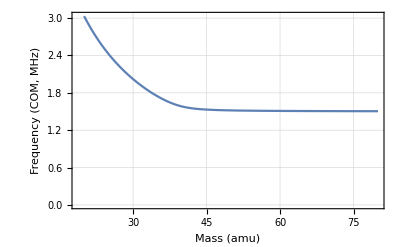
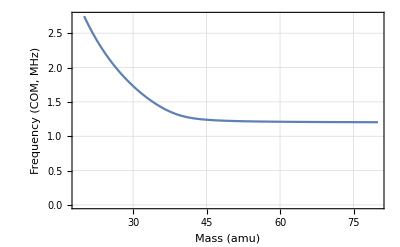
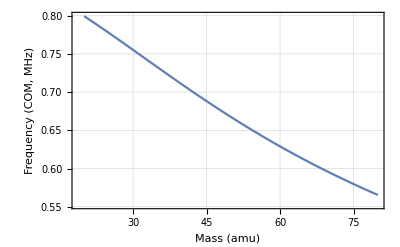
{{ | Mass (AMU) | Mode Frequencies (MHz)
EGGS | 195.0 | (1.4236
1.08508
0.336268)
RF | 35.7 | (1.7122
1.4236
0.729144)
Axial | -14.0 | (31.6884
31.416
0.88469)Dark Ion Candidates: , | Axial COM | RF COM | EGGS COM
AMU 25 | 0.777766 | 2.13539 | 2.42275
AMU 26 | 0.773306 | 2.04142 | 2.32942
AMU 27 | 0.768818 | 1.9546 | 2.24318
AMU 28 | 0.764307 | 1.87423 | 2.16332
AMU 29 | 0.759778 | 1.7997 | 2.08924
AMU 36 | 0.727942 | 1.41295 | 1.70131
AMU 37 | 0.723425 | 1.3759 | 1.66325
AMU 38 | 0.718927 | 1.34385 | 1.63022
AMU 39 | 0.714451 | 1.31699 | 1.60268
AMU 40 | 0.71 | 1.2952 | 1.5808
AMU 41 | 0.705577 | 1.27801 | 1.56418
AMU 43 | 0.696823 | 1.25439 | 1.54289
AMU 53 | 0.655361 | 1.21761 | 1.51439
AMU 54 | 0.651452 | 1.21631 | 1.51348
AMU 55 | 0.647589 | 1.21515 | 1.51268
AMU 56 | 0.643772 | 1.21413 | 1.51197Typical Masses},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
{{massTable,typicalResultsTable},resPlots}
```

## Extra

```mathematica
Sqrt[#1/#2]*#3&[1405.6,1572.5,51.5]
```

48.6903

```mathematica
(*get arbitrary mode values*)
arbModeVals=MotionalModes@@mystParamsXYZ[{40.,40.}];
{arbModeVals[[1]]/wmhz//MatrixForm,arbModeVals[[2]]/((*wmhz*)1)//MatrixForm}
```

{(1.5808 | 1.41238
1.2952 | 1.08326
1.22976 | 0.71),((0.707107
0.707107) | (-0.707107
0.707107)
(0.707107
0.707107) | (-0.707107
0.707107)
(-0.707107
0.707107) | (-0.707107
-0.707107))}

```mathematica
(*get arbitrary mode values*)
arbModeVals=MotionalModes@@mystParamsXYZ[{40.,25}];
{arbModeVals[[1]]/wmhz//MatrixForm,arbModeVals[[2]]/((*wmhz*)1)//MatrixForm}
```

{(2.42275 | 1.48957
2.13539 | 1.18028
1.42 | 0.777766),((0.0876638
0.99615) | (-0.99615
0.0876638)
(0.101195
0.994867) | (-0.994867
0.101195)
(-0.534522
0.845154) | (-0.845154
-0.534522))}

```mathematica
(*mystParamsXYZ[{40.,36.}]*)
```

```mathematica
(*(*get arbitrary mode values*)
arbModeVals=MotionalModes@@mystParamsXYZ[{40.,36.}];
arbModeVals[[1]]/wmhz//MatrixForm*)
```

```mathematica
(*(*guess COM mode frequencies for arbitrary mass*)
FrequencyPredict[28.]//MatrixForm*)
```